# Thermalization from quenching in coupled oscillators

## M. Harinarayanan

## Mentor: Dr. Karthik Rajeev

This notebook presents the codes used for the calculations and plots in the work Thermalization from Quenching in Coupled Oscillators. The study employs a simple model consisting of two coupled quantum harmonic oscillators, initially prepared in their ground state, to demonstrate quench-induced finite-time thermalization. Specifically, we examine how the reduced density matrix of one oscillator evolves towards a thermal state under this setup. Owing to the Gaussian character of the dynamics, the evolution is greatly simplified, reducing the problem to just three equations. These equations determine three tunable parameters, enabling the approximation of any desired target temperature with arbitrary precision.

## A. Section II: REVIEW OF TWO-MODE GAUSSIAN PURE STATES

```mathematica
ClearAll["Global`*"]
```

### Undisplaced two mode Gaussian pure state

Here we consider a pure, undisplaced Gaussian wavefunction of a two-oscillator system of the form

```mathematica
ψ[x1_,x2_]=N1 Exp[-1/2(A11 x1^2+A22 x2^2+2A12 x1 x2) ]
```

ⅇ^(1/2 (-A11 x1^2-2 A12 x1 x2-A22 x2^2)) N1

```mathematica
ψst[x1_,x2_]=N1 Exp[-1/2(A11st x1^2+A22st x2^2+2A12st x1 x2) ]
```

ⅇ^(1/2 (-A11st x1^2-2 A12st x1 x2-A22st x2^2)) N1

To get the normalization, we compute the norm^2 as

```mathematica
Integrate[ψ[x1,x2]ψst[x1,x2],{x1,-Infinity,Infinity},{x2,-Infinity,Infinity}]
```

ConditionalExpression[(2 N1^2 π)/(√(A22+A22st) √(A11+A11st-(A12+A12st)^2/(A22+A22st))), Re[(A12^2+2 A12 A12st+A12st^2-(A11+A11st) (A22+A22st))/(A22+A22st)]<0]

This leads to

```mathematica
N1=FullSimplify[((√(A22+A22st) √(A11+A11st-(A12+A12st)^2/(A22+A22st)))/(2π))^(1/2),Assumptions->A11+A11st>0&&A22+A22st>0]
```

(((A22+A22st) (A11+A11st-(A12+A12st)^2/(A22+A22st)))^(1/4))/(√(2 π))

### Reduced density matrix

The reduced density matrix can be found by partial tracing, which leads to

```mathematica
ρ1[x1p_,x1_]=Integrate[ψ[x1,x2]ψst[x1p,x2],{x2,-Infinity,Infinity}]
```

ConditionalExpression[(√((A22+A22st) (A11+A11st-(A12+A12st)^2/(A22+A22st))) ⅇ^((A12^2 x1^2-A11 (A22+A22st) x1^2+2 A12 A12st x1 x1p+(A12st^2-A11st (A22+A22st)) x1p^2)/(2 (A22+A22st))))/(√(A22+A22st) √(2 π)), Re[A22+A22st]>0]

To read-off X,Y,Z variables collect the different terms in the exponential

```mathematica
Collect[-2/(m ω)(1/(2 (A22+A22st))(A12^2 x1^2-A11 (A22+A22st) x1^2+2 A12 A12st x1 x1p+(A12st^2-A11st (A22+A22st)) x1p^2)),{x1^2,x1p^2,x1 x1p},FullSimplify]
```

((-A12^2+A11 (A22+A22st)) x1^2)/((A22+A22st) m ω)+((-A12st^2+A11st (A22+A22st)) x1p^2)/((A22+A22st) m ω)-(2 A12 A12st x1 x1p)/(A22 m ω+A22st m ω)

Hence, X - i Y is

```mathematica
(-A12^2+A11 (A22+A22st))/((A22+A22st) m ω)
```

(-A12^2+A11 (A22+A22st))/((A22+A22st) m ω)

or

```mathematica
{X,Y}={(-ReA12sqr+2ReA11 (ReA22))/(2(ReA22) m ω),-(-ImA12sqr+2ImA11 (ReA22))/(2(ReA22) m ω)}//FullSimplify
```

{-(ReA12sqr-2 ReA11 ReA22)/(2 m ReA22 ω),(ImA12sqr-2 ImA11 ReA22)/(2 m ReA22 ω)}

and Z is

```mathematica
Z=-(2 (ReA12^2+ImA12^2))/(2(ReA22 m ω))*1/2//FullSimplify
```

-(ImA12^2+ReA12^2)/(2 m ReA22 ω)

Let us rewrite the density matrix now as

```mathematica
ρ[x1p_,x1_]=N2 Exp[-m ω/2((X1+I Y1)x1p^2+(X1-I Y1)x1^2+2Z1 x1p x1)]
```

ⅇ^(-1/2 m (x1^2 (X1-ⅈ Y1)+x1p^2 (X1+ⅈ Y1)+2 x1 x1p Z1) ω) N2

The normalization condition requires

```mathematica
Integrate[ρ[x,x],{x,-Infinity,Infinity}]
```

ConditionalExpression[(N2 √π)/(√(m (X1+Z1) ω)), Re[m (X1+Z1) ω]>0]

be unity, which implies

```mathematica
N2=((√π)/(√(m (X1+Z1) ω)))^-1
```

(√(m (X1+Z1) ω))/(√π)

### Covariance matrix

To find <x1^2> in terms of X, Y and Z, we compute

```mathematica
Σxx=Integrate[x^2 ρ[x,x],{x,-Infinity,Infinity}]
```

ConditionalExpression[1/(2 m (X1+Z1) ω), Re[m (X1+Z1) ω]>0]

To find <p1^2> , given by ∫ ψ*(x) (-ℏ^2 ψ’’(x))dx,  in terms of X, Y and Z, we compute the differential, and then integrate the expression.

```mathematica
-D[ρ[xp,x],{x,2}]/.{xp-> x}//FullSimplify
```

(ⅇ^(-m x^2 (X1+Z1) ω) m ω √(m (X1+Z1) ω) (X1-ⅈ Y1-m x^2 (X1-ⅈ Y1+Z1)^2 ω))/(√π)

Now, we integrate the full expression :

```mathematica
Σpp=Integrate[(ⅇ^(-m x^2 (X1+Z1) ω) m ω √(m (X1+Z1) ω) (X1-ⅈ Y1-m x^2 (X1-ⅈ Y1+Z1)^2 ω))/(√π),{x,-Infinity,Infinity}]
```

ConditionalExpression[(m (X1^2+Y1^2-Z1^2) ω)/(2 (X1+Z1)), Re[m (X1+Z1) ω]>0]

To find <x1 p1> , given by ∫ ψ*(x) (x (-i ℏ ψ’(x)))dx, in terms of X, Y and Z, we compute

```mathematica
xp D[ρ[xp,x],x]/.{xp-> x}//FullSimplify
```

-(ⅇ^(-m x^2 (X1+Z1) ω) m x^2 (X1-ⅈ Y1+Z1) ω √(m (X1+Z1) ω))/(√π)

Now, we integrate the full expression:

```mathematica
Σxp=Integrate[ -I  (-(ⅇ^(-m x^2 (X1+Z1) ω) m x^2 (X1-ⅈ Y1+Z1) ω √(m (X1+Z1) ω))/(√π)),{x,-Infinity,Infinity}]//FullSimplify
```

ConditionalExpression[1/2 (ⅈ+Y1/(X1+Z1)), Re[m (X1+Z1) ω]>0]

To find < p1 x1> , given by ∫ ψ*(x) ((-i ℏ) (x ψ(x))’)dx, in terms of X, Y and Z, we compute:

```mathematica
D[ x ρ[xp,x],x]/.{xp->x }//FullSimplify
```

(ⅇ^(-m x^2 (X1+Z1) ω) √(m (X1+Z1) ω) (1-m x^2 (X1-ⅈ Y1+Z1) ω))/(√π)

Now, we integrate the full expression:

```mathematica
Σpx=Integrate[ -I ((ⅇ^(-m x^2 (X1+Z1) ω) √(m (X1+Z1) ω) (1-m x^2 (X1-ⅈ Y1+Z1) ω))/(√π)),{x,-Infinity,Infinity}]//FullSimplify
```

ConditionalExpression[1/2 (-ⅈ+Y1/(X1+Z1)), Re[m (X1+Z1) ω]>0]

So the covariance matrix  of our system becomes,

```mathematica
Σ={{Σxx,Σxp},{Σpx,Σpp}} //FullSimplify
```

{{ConditionalExpression[1/(2 m X1 ω+2 m Z1 ω), Re[m (X1+Z1) ω]>0],ConditionalExpression[1/2 (ⅈ+Y1/(X1+Z1)), Re[m (X1+Z1) ω]>0]},{ConditionalExpression[1/2 (-ⅈ+Y1/(X1+Z1)), Re[m (X1+Z1) ω]>0],ConditionalExpression[(m (X1^2+Y1^2-Z1^2) ω)/(2 (X1+Z1)), Re[m (X1+Z1) ω]>0]}}

```mathematica
MatrixForm[Σ]
```

(ConditionalExpression[1/(2 m X1 ω+2 m Z1 ω), Re[m (X1+Z1) ω]>0] | ConditionalExpression[1/2 (ⅈ+Y1/(X1+Z1)), Re[m (X1+Z1) ω]>0]
ConditionalExpression[1/2 (-ⅈ+Y1/(X1+Z1)), Re[m (X1+Z1) ω]>0] | ConditionalExpression[(m (X1^2+Y1^2-Z1^2) ω)/(2 (X1+Z1)), Re[m (X1+Z1) ω]>0])

### R-Space Variables

The dynamics of the density matrix can fully be described by these three parameters  X, Y, and Z. These parameters vary with time, so the evolution of the density matrix can be represented conveniently by a three-dimensional curve R(t)= ( X(t), Y(t), Z(t) ).

The general thermal state of a harmonic oscillator, at an inverse temperature β,  is given by the equation,

```mathematica
ρβ[x1p_,x1_]= Nβ Exp[(-m ω)/2((x1^2+ x1p^2)Coth[β ω] - 2 x1 x1p Csch[β ω])]//FullSimplify
```

ⅇ^(-1/2 m (x1^2+x1p^2) ω Coth[β ω]+m x1 x1p ω Csch[β ω]) Nβ

As the oscillator reaches thermal equilibrium,  ρ [x1p_,x1_] approaches ρβ [x1p_,x1_]. Comparing, we get R_β = ( Coth[β ω], 0, -Csch[β ω] ). We can visualize the set of density matrices, for temperatures, in R space with the following codes:

### Figure 1:

Here we will plot the collection of possible thermal states for oscillator-1 at different temperatures. For the purpose of plotting, we set the frequency to be unity.

```mathematica
ωplot1=1
```

1

```mathematica
Show[ParametricPlot3D[{Coth[ωplot1/T],0,-Csch[ωplot1/T]},{T,0,5},Ticks->None,PlotStyle->{Thick,Red},AxesLabel->{"X","Y","Z"}],Graphics3D[{Blue,PointSize[Large],Point[{1,0,0}]}],Graphics3D[{Opacity[0.1,Red],InfinitePlane[{{0,0,0},{1,0,0},{0,0,1}}]}],Graphics3D[{Red,Arrow[{{Coth[ωplot1/4.9],0,-Csch[ωplot1/4.9]},{Coth[ωplot1/5],0,-Csch[ωplot1/5]}}]}],LabelStyle->Black]
```

-Graphics3D-

The family of thermal density matrices is represented by the curve R_β = (Coth[β ω], 0, −Csch[β ω]).  The curve lies entirely in the X–Z plane, shown as the shaded region.The blue dot indicates the ground state, and the arrow shows the direction of increasing temperature.

## B. Section III: THE SET UP

### Hamiltonian of the System

We consider the system of two coupled oscillators is described by a Hamiltonian of the form:

```mathematica
H=p1^2/(2 m) + p2^2/(2m)+1/2 m Ω^2 x1^2+1/2 m Ω^2 x2^2+1/2 Κ[t](x1-x2)^2
```

p1^2/(2 m)+p2^2/(2 m)+1/2 m x1^2 Ω^2+1/2 m x2^2 Ω^2+1/2 (x1-x2)^2 Κ[t]

where Κ is the coupling, and Ω is the frequency of the oscillators. Our coupling is turned on from t=0 to t-T, and is off otherwise. So the time dependence of both coupling and frequency is as follows:

```mathematica
Κ[t_]=Piecewise[{{k,0<t<τ}},0]
```

Piecewise[{{k, 0<t<τ}, {0, True}}]

```mathematica
Ω[t_]=Piecewise[{{ω,t<0||t>τ},{ωp,0<t<τ}}]
```

Piecewise[{{ω, t<0||t>τ}, {ωp, 0<t<τ}, {0, True}}]

### Figure 2: Variation of equipotential surface of the system during passive and active phase

Here, we will look at the For the purpose of plotting, we set the parameters to arbitrary constants:

```mathematica
{Ω1plot2,Ω2plot2,Kplot2}={1,1.1,2}
```

{1,1.1,2}

The potentials before and coupling are:

```mathematica
V0[x1_,x2_]=1/2 Ω1plot2^2(x1^2+x2^2)
```

1/2 (x1^2+x2^2)

```mathematica
V[x1_,x2_]=1/2 Ω2plot2^2 (x1^2+x2^2)+1/2 Kplot2(x1-x2)^2
```

(x1-x2)^2+0.605 (x1^2+x2^2)

Let us call the plots for the two potentials as p1 and p2. Then,

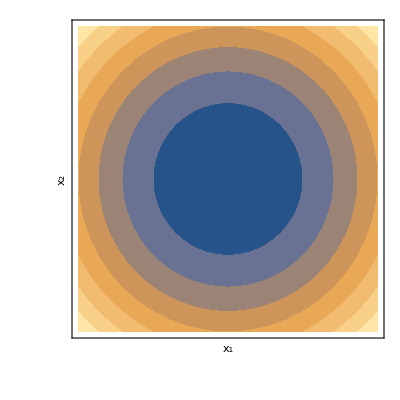

```mathematica
p1=ContourPlot[V0[x1,x2],{x1,-2,2},{x2,-2,2},ContourStyle->None,FrameLabel->{"x_1","x_2"},LabelStyle->{Black},FrameTicks->False]
```

This is the contour representation of the effective 2D potential of the coupled oscillator system, for typical values of ω’/ω  and k/ω^2, when the system is in the uncoupled phase.

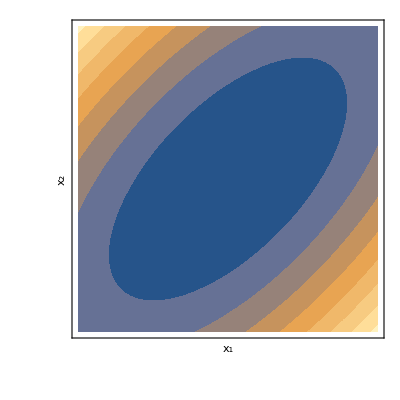

```mathematica
p1=ContourPlot[V[x1,x2],{x1,-2,2},{x2,-2,2},ContourStyle->None,FrameLabel->{"x_1","x_2"},LabelStyle->{Black},FrameTicks->False]
```

This is the contour representation of the effective 2D potential of the coupled oscillator system, for typical values of ω’/ω  and k/ω^2, when the system is in the coupled phase.

### The Ermakov Equations

Let us consider a Gaussian wavefunction ψDiag = Exp[-m/(2 hbar)(Aplus*xplus^2+ Aminus*xminus^2) ]  of the system. We define the diagonalized quadratic phase coefficients of the  wavefunction Aplus = (-i m)/hbar(μplus'/μplus) and Aminus = (-i m)/hbar(μminus'/μminus) .   Substituting this Gaussian ansatz into the Schrodinger equation and simplifying, we find that μplus and μminus satisfies the classical harmonic oscillator equation μ’’ + ω^2 μ = 0.

```mathematica
μ[t]=b[t] Exp[I θ[t]]
```

ⅇ^(ⅈ θ[t]) b[t]

Putting this value into the classical oscillator equation,

```mathematica
D[μ[t],{t,2}]+ω^2 μ[t]==0//FullSimplify
```

ⅇ^(ⅈ θ[t]) (2 ⅈ b'[t] θ'[t]+b''[t]+b[t] (ω^2-θ'[t]^2+ⅈ θ''[t]))==0

Let us divide this equation by ⅇ^(ⅈ θ[t]) and then separate the real and imaginary parts.  The real part becomes,

```mathematica
b''[t]+b[t] (ω^2-θ'[t]^2)==0//FullSimplify
```

ω^2 b[t]+b''[t]==b[t] θ'[t]^2

and imaginary part is

```mathematica
2 b'[t] θ'[t]+b[t] θ''[t]==0//FullSimplify
```

2 b'[t] θ'[t]+b[t] θ''[t]==0

The LHS of the equation is nothing but 1/b d/dt(θ' b^2). This gives  θ’= c/b^2, where c is a constant.  Substituting this value of θ’ into the real part, we get  ω^2 b[t]+b''[t]-c^2/b[t]^3=0. This is the Ermakov equation.  Let us now demand that the wavefunction approaches the local ground state at  t=0 as t -> 0. This implies,

```mathematica
{b[0],b'[0],θ'[0],c}={1,0,ω[0],ω[0]}
```

{1,0,ω[0],ω[0]}

So the Ermakov equation becomes  b''+b ω^2=(ω(0)^2)/b^3.

### Expressions for bplus and bminus

The solution of μ when the system is initially at ground state, when t -> -∞, can be called μin and when the system approaches ground state, as t -> +, can be called μout. So the solutions take the values:

```mathematica
{μleft,μright}={Exp[I ωminus t],a1 Exp[I ωplus t]+b1 Exp[-I ωplus t]}
```

{ⅇ^(ⅈ t ωminus),b1 ⅇ^(-ⅈ t ωplus)+a1 ⅇ^(ⅈ t ωplus)}

```mathematica
{μleftdot,μrightdot}={D[μleft,t],D[μright,t]}
```

{ⅈ ⅇ^(ⅈ t ωminus) ωminus,-ⅈ b1 ⅇ^(-ⅈ t ωplus) ωplus+ⅈ a1 ⅇ^(ⅈ t ωplus) ωplus}

Using the continuity of μ and μdot, we can find the values of a1 and b1.

```mathematica
Solve[{μleft==μright,μleftdot==μrightdot},{a1,b1}]/.t->0
```

{{a1→(ωminus+ωplus)/(2 ωplus),b1→(-ωminus+ωplus)/(2 ωplus)}}

Furthermore, we define μ(t) = b(t) e^iθ. Equating the condition | μ |^2=|b|^2, we solve for b.

```mathematica
{μreal,μimaginary}=ComplexExpand[ReIm[(ⅇ^(-ⅈ t ωplus) (-ωminus+ωplus))/(2 ωplus)+(ⅇ^(ⅈ t ωplus) (ωminus+ωplus))/(2 ωplus)]]//FullSimplify
```

{Cos[t ωplus],(ωminus Sin[t ωplus])/ωplus}

Note that we have μplus and μminus for the two normal modes. For μplus, ωminus = ω, and ωplus = ωp. For μminus, ωminus = ω and and ωplus =√(ωp^2+ 2k). If we define η = √(1+(2 k)/ωp^2), we can write

```mathematica
η=√(1+(2 k)/ωp^2)
```

√(1+(2 k)/ωp^2)

From μplus and μminus, we will have the corresponding values for b, They can be called bplus and bminus for the two normal modes. bplus=√(|μplus|^2) and bminus=√(|μminus|^2) :

```mathematica
{bplus,bminus}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2))}//FullSimplify
```

{√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2))}

Taking their time derivatives, we get bplusdot and bminusdot.

```mathematica
{bplusdot,bminusdot}={D[bplus,t],D[bminus,t]}//FullSimplify
```

{((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}

Now, the  argument of the exponential of the wavefunction can be written as

```mathematica
SInitial=-1/2(A11 x1^2+A22 x2^2+2A12 x1 x2)/.{x1->(xPlus+xMinus)/(√2),x2->(xPlus-xMinus)/(√2)}//FullSimplify
```

1/4 (-A11 (xMinus+xPlus)^2+(xMinus-xPlus) (A22 (-xMinus+xPlus)+2 A12 (xMinus+xPlus)))

The  argument of the exponential in the diagonalized wavefunction ψDiag can be defined as,

```mathematica
SDiag=-APlus/2 xPlus^2-AMinus/2 xMinus^2 //FullSimplify
```

1/2 (-AMinus xMinus^2-APlus xPlus^2)

```mathematica
Collect[SInitial,{xPlus^2,xMinus^2,x1Plus xMinus},FullSimplify]
```

1/4 (-A11+2 A12-A22) xMinus^2+1/2 (-A11+A22) xMinus xPlus+1/4 (-A11-2 A12-A22) xPlus^2

Comparing the coefficients, we get,

```mathematica
Solve[{-AMinus/2==1/4 (-A11+2 A12-A22),-APlus/2==1/4 (-A11-2 A12-A22)},{APlus,AMinus}]/.A22->A11//FullSimplify
```

{{APlus→A11+A12,AMinus→A11-A12}}

But Aplus = (-i m)/hbar(μplus'/μplus) and Aminus = (-i m)/hbar(μminus'/μminus).

```mathematica
Clear[μplus,μminus,bplus,bminus,θ,t]
```

```mathematica
{μplus,μminus}={bplus[t] Exp[I θ[t]],bminus[t] Exp[I θ[t]]}
```

{ⅇ^(ⅈ θ[t]) bplus[t],ⅇ^(ⅈ θ[t]) bminus[t]}

```mathematica
{μplusdot,μminusdot}={D[μplus,t],D[μminus,t]}
```

{ⅇ^(ⅈ θ[t]) bplus'[t]+ⅈ ⅇ^(ⅈ θ[t]) bplus[t] θ'[t],ⅇ^(ⅈ θ[t]) bminus'[t]+ⅈ ⅇ^(ⅈ θ[t]) bminus[t] θ'[t]}

```mathematica
{Aplus,Aminus}={-I μplusdot/μplus,-I μminusdot/μminus}//FullSimplify
```

{-(ⅈ bplus'[t])/bplus[t]+θ'[t],-(ⅈ bminus'[t])/bminus[t]+θ'[t]}

Now we have Aplus and Aminus. But θ’ = ω. So,

```mathematica
Solve[{-(ⅈ bplus'[t])/bplus[t]+ω==A11+A12,-(ⅈ bminus'[t])/bminus[t]+ω==A11-A12},{A11,A12}]//FullSimplify
```

{{A11→ω-(ⅈ bminus'[t])/(2 bminus[t])-(ⅈ bplus'[t])/(2 bplus[t]),A12→1/2 ⅈ (bminus'[t]/bminus[t]-bplus'[t]/bplus[t])}}

Or equivalently we can write,

```mathematica
{A11,A12,A22}={(ω/(2 bplus^2)-I bplusdot/(2bplus)+ω/(2 bminus^2)-I bminusdot/(2bminus)),(ω/(2 bplus^2)-I bplusdot/(2bplus)-(ω/(2 bminus^2)-I bminusdot/(2bminus))),(ω/(2 bplus^2)-I bplusdot/(2bplus)+ω/(2 bminus^2)-I bminusdot/(2bminus))}//FullSimplify
```

{ω/(2 bminus^2)+ω/(2 bplus^2)+(ⅈ (-ω+ωp) (ω+ωp) Sin[2 t ωp])/(4 bplus ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2))+(ⅈ (2 k-ω^2+ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(4 bminus √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2))),-ω/(2 bminus^2)+ω/(2 bplus^2)+(ⅈ (-ω+ωp) (ω+ωp) Sin[2 t ωp])/(4 bplus ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2))+(ⅈ (-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(4 bminus √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2))),ω/(2 bminus^2)+ω/(2 bplus^2)+(ⅈ (-ω+ωp) (ω+ωp) Sin[2 t ωp])/(4 bplus ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2))+(ⅈ (2 k-ω^2+ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(4 bminus √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}

And their complex conjugates as:

```mathematica
{A11st,A22st,A12st}={ω/(2 bplus^2)+I bplusdot/(2bplus)+ω/(2 bminus^2)+I bminusdot/(2bminus),ω/(2 bplus^2)+I bplusdot/(2bplus)+ω/(2 bminus^2)+I bminusdot/(2bminus),ω/(2 bplus^2)+I bplusdot/(2bplus)-(ω/(2 bminus^2)+I bminusdot/(2bminus))}//FullSimplify
```

{ω/(2 bminus^2)+ω/(2 bplus^2)+(ⅈ (ω-ωp) (ω+ωp) Sin[2 t ωp])/(4 bplus ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2))+(ⅈ (-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(4 bminus √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2))),ω/(2 bminus^2)+ω/(2 bplus^2)+(ⅈ (ω-ωp) (ω+ωp) Sin[2 t ωp])/(4 bplus ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2))+(ⅈ (-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(4 bminus √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2))),-ω/(2 bminus^2)+ω/(2 bplus^2)+(ⅈ (ω-ωp) (ω+ωp) Sin[2 t ωp])/(4 bplus ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2))+(ⅈ (2 k-ω^2+ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(4 bminus √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}

### Figure 3: Evolution of the density matrix for randomly chosen values

Here we plot an arbitrary (uncontrolled) evolution of the oscillator, for arbitrary values of k, ω, and ωp.

Recall:

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}

Now we can obtain the real and imaginary parts of A_ij for the particular values k=1, ω=1, and ωp=2.

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}/.{k->1,ω->1,ωp->2}//FullSimplify
```

{4/(5+3 Cos[4 t])-6/(7+5 Cos[2 √6 t]),(3 Sin[4 t])/(5+3 Cos[4 t])-(5 √(3/2) Sin[2 √6 t])/(7+5 Cos[2 √6 t])}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}/.{k->1,ω->1,ωp->2}//FullSimplify
```

{4/(5+3 Cos[4 t])+6/(7+5 Cos[2 √6 t]),(3 Sin[4 t])/(5+3 Cos[4 t])+(5 √(3/2) Sin[2 √6 t])/(7+5 Cos[2 √6 t]),4/(5+3 Cos[4 t])+6/(7+5 Cos[2 √6 t]),(3 Sin[4 t])/(5+3 Cos[4 t])+(5 √(3/2) Sin[2 √6 t])/(7+5 Cos[2 √6 t])}

The real and imaginary terms of  A_12^2  is given by:

```mathematica
ReA12sqr=(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)/(4 bminus^4 bplus^4)/.{k->1,ω->1,ωp->2}//FullSimplify
```

(2 (2 (1+9 Cos[4 t]-10 Cos[2 √6 t])^2-3/4 (√6 (7+5 Cos[2 √6 t]) Sin[4 t]-5 (5+3 Cos[4 t]) Sin[2 √6 t])^2))/((5+3 Cos[4 t])^2 (7+5 Cos[2 √6 t])^2)

```mathematica
ImA12sqr=-((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3)/.{k->1,ω->1,ωp->2}//FullSimplify
```

-(((1+9 Cos[4 t]-10 Cos[2 √6 t]) (84 Sin[4 t]-50 √6 Sin[2 √6 t]-15 (-2+√6) Sin[2 (2+√6) t]+15 (2+√6) Sin[4 t-2 √6 t]))/((5+3 Cos[4 t])^2 (7+5 Cos[2 √6 t])^2))

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//FullSimplify
```

{(926+42 Cos[4 t]-50 Cos[2 √6 t]-15 (5+2 √6) Cos[2 (-2+√6) t]+15 (-5+2 √6) Cos[2 (2+√6) t])/(16 (29+9 Cos[4 t]+10 Cos[2 √6 t])),(2 (9 Sin[4 t]+5 √6 Sin[2 √6 t]))/(29+9 Cos[4 t]+10 Cos[2 √6 t]),(-158-42 Cos[4 t]+50 Cos[2 √6 t]+15 (5+2 √6) Cos[2 (-2+√6) t]+15 (5-2 √6) Cos[2 (2+√6) t])/(16 (29+9 Cos[4 t]+10 Cos[2 √6 t]))}

Here, we consider the evolution for a time interval T = 20.

```mathematica
T=20
```

20

Now the initial values of X, Y, and Z, when when t=0 be Xi, Yi, and Zi.

```mathematica
{Xi,Yi,Zi}={X,Y,Z}/.t->0//FullSimplify
```

{1,0,0}

And the final values of X, Y, and Z, when when t=T be Xf, Yf, and Zf.

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->T//FullSimplify
```

{(463+21 Cos[80]-25 (1+3 Cos[80]) Cos[40 √6]-30 √6 Sin[80] Sin[40 √6])/(8 (29+9 Cos[80]+10 Cos[40 √6])),(2 (9 Sin[80]+5 √6 Sin[40 √6]))/(29+9 Cos[80]+10 Cos[40 √6]),(-79-21 Cos[80]+25 (1+3 Cos[80]) Cos[40 √6]+30 √6 Sin[80] Sin[40 √6])/(8 (29+9 Cos[80]+10 Cos[40 √6]))}

```mathematica
Show[{ParametricPlot3D[{X,Y,Z},{t,0,T},PlotStyle->Black,BoxRatios->{1, 1, 1},Ticks->None,AxesLabel->{"X","Y","Z"}]},{ParametricPlot3D[{Coth[θ],0,-Csch[θ]},{θ,0,10},PlotStyle->Red],Graphics3D[{Blue,PointSize[0.03],Point[{Xi,Yi,Zi}],Green,PointSize[0.03],Point[{Xf,Yf,Zf}]}]},LabelStyle->Black]
```

-Graphics3D-

This represents the evolution of ρ^(1)(x1 x’1) represented in the R-space, assuming a randomly chosen set of the tunable parameters ω’, k and τ. The oscillator-1 is initially in the ground state (blue dot) and evolves, at t = τ, to the green point. The red curve is the family of thermal states.

## C. SECTION IV: THERMALIZATION FROM QUENCHING

### Figure 4: The Energy-Frequency diagram

Now let us look at the energy frequency diagram of the oscillator when it undergoes our protocol. We will represent the dimensionless frequency parameter  ωtilde=ω'/ω  on x-axis, and the ratio of average energy and ground state, U_β/E_g on y-axis.

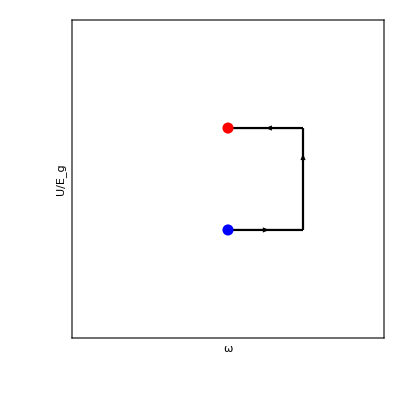

```mathematica
Show[{ContourPlot[y==1,{x,0,1},{y,-3,3},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}},FrameLabel->{"ω",Rotate["U/E_g",-π/2]},LabelStyle->{Black},FrameTicks->False],ContourPlot[x==1,{x,-1,2},{y,1,-1},ContourStyle->Black],ContourPlot[y==-1,{x,0,1},{y,-3,3},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}],Graphics[{Black,Arrowheads[0.03],Arrow[{{0.6,1},{0.5,1}}],Arrow[{{1,0},{1,0.5}}],Arrow[{{0.5,-1},{0.55,-1}}]}],Graphics[{Blue,PointSize[0.02],Point[{0,-1}]}],Graphics[{Red,PointSize[0.02],Point[{0,1}]}]}]
```

This is the energy-frequency diagram for oscillator-1 as it undergoes the protocol.

### Defining Dimensionless Parameters

```mathematica
ClearAll[ω,ωp,k,τ]
```

For convenience, we introduce the dimensionless parameters ωptilde, ktilde, and τtilde, such that:

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2 ,(2π τtilde)/ω }
```

{ω ωtilde,ktilde ω^2,(2 π τtilde)/ω}

### A. Special discrete set of thermal states

The three equations that describe the dynamics of the oscillator are analytically unsolvable for arbitrary temperatures. However, exact analytic solutions exist for a special discrete set (SDS) of temperatures.  This SDS temperatures require  the condition that the two normal mode frequencies are commensurate (p/q, where p and q are integers). Furthermore,  if p and q are odd integers,  we get:

```mathematica
ClearAll[η,ω,ωp,k,bplus,bminus,bminusdot,bplusdot]
```

```mathematica
τtilde==(2l+1)/(4ωtilde)==(2n+1)/(4 √(ωtilde^2+2ktilde))
```

τtilde==(1+2 l)/(4 ωtilde)==(1+2 n)/(4 √(2 ktilde+ωtilde^2))

```mathematica
ηdimensionless==(√(ωtilde^2+2ktilde))/ωtilde==(2n+1)/(2l+1)
```

ηdimensionless==(√(2 ktilde+ωtilde^2))/ωtilde==(1+2 n)/(1+2 l)

Now, we redefine the real and imaginary parts of A_ij .

```mathematica
{ReA12sqr,ReA11,ImA11,ReA22,ImA22}={(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)/(4 bminus^4 bplus^4),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}
```

{(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)/(4 bminus^4 bplus^4),ω/(2 bminus^2)+ω/(2 bplus^2),-bminusdot/(2 bminus)-bplusdot/(2 bplus),ω/(2 bminus^2)+ω/(2 bplus^2),-bminusdot/(2 bminus)-bplusdot/(2 bplus)}

```mathematica
ReA12sqr/(2ReA22)-ReA11//FullSimplify
```

-(bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^4+6 bminus^2 bplus^2+bplus^4) ω^2)/(4 bminus^2 bplus^2 (bminus^2+bplus^2) ω)

If we write the density matrix as rho1 ∝ Exp[-γ/2 (x1^2 + x1'^2) + δ x1 x1’], the coefficient of x^2 in the Gaussian density matrix is 1/2[Re[A12^2]/(2Re[A22])-Re[A11]]. Then  -γ/2 would be equal to 1/2(-((bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^4+6 bminus^2 bplus^2+bplus^4) ω^2)/(4 bminus^2 bplus^2 (bminus^2+bplus^2) ω))).

```mathematica
{bminus,bplus}={ω/ωp,ω/(ωp η)}//FullSimplify
```

{ω/ωp,ω/(η ωp)}

For the SDS, bplus and bminus are constants in time.

```mathematica
{bminusdot,bplusdot}={0,0}
```

{0,0}

```mathematica
γ=(bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^4+6 bminus^2 bplus^2+bplus^4) ω^2)/(4 bminus^2 bplus^2 (bminus^2+bplus^2) ω)//FullSimplify
```

((1+6 η^2+η^4) ωp^2)/(4 (1+η^2) ω)

Similarly, the coefficient of x x’ δ is equal to Re[A12^2]/(2 Re[A11])

```mathematica
{ReA12sqr,ReA11}//FullSimplify
```

{((-1+η^2)^2 ωp^4)/(4 ω^2),((1+η^2) ωp^2)/(2 ω)}

```mathematica
δ=ReA12sqr/(2 ReA11)//FullSimplify
```

((-1+η^2)^2 ωp^2)/(4 (1+η^2) ω)

Comparing to the general thermal state of a harmonic oscillator, we get γ/δ = Cosh[βω]  and  δ = Cosech[βω]. Consequently, we get:

```mathematica
{(η^4+6 η^2+1)/((η^2-1)^2),(4 (η^2+1))/(ωtilde^2 (η^2-1)^2)}=={Cosh[ω β],Sinh[ω β]}
```

{(1+6 η^2+η^4)/((-1+η^2)^2),(4 (1+η^2))/((-1+η^2)^2 ωtilde^2)}=={Cosh[β ω],Sinh[β ω]}

Now we can obtain the expression for η

```mathematica
Solve[(1+6 η^2+η^4)/((-1+η^2)^2)==Cosh[β ω],η]
```

{{η→-Coth[(β ω)/4]},{η→Coth[(β ω)/4]},{η→-Tanh[(β ω)/4]},{η→Tanh[(β ω)/4]}}

So η = 1/ωtilde^2 = [Tanh[β ω] ]^(±1)  =  (2n+1)/(2l+1).  Here,  β ω = E_g/(k_B T). Therefore :E_g/(k_B T)= { 2 ArcTanh[(2n+1)/(2l+1)] ,  2 ArcCoth [(2n+1)/(2l+1)] } = log ((n+l+1)/(|n-l|)) . We can call this special discrete set of inverse temperatures βSDS. We also get ωptilde=√((2l+1)/(2n+1)).  Since η=√(ω' +2k)/ω',  we get:

```mathematica
η={-Coth[(β ω)/4],Coth[(β ω)/4],-Tanh[(β ω)/4],Tanh[(β ω)/4]}
```

{-Coth[(β ω)/4],Coth[(β ω)/4],-Tanh[(β ω)/4],Tanh[(β ω)/4]}

```mathematica
k=(ω^2/2) (η-1/η)//Simplify
```

{-ω^2 Csch[(β ω)/2],ω^2 Csch[(β ω)/2],ω^2 Csch[(β ω)/2],-ω^2 Csch[(β ω)/2]}

```mathematica
βSDS=1/Eg Log[(n+l+1)/Abs[n-l]]
```

Log[(1+l+n)/Abs[-l+n]]/Eg

```mathematica
ωtilde= Sqrt[(2l+1)/(2n+1)]
```

√((1+2 l)/(1+2 n))

```mathematica
Solve[(ωtilde^2+2ktilde)/ωtilde^2==1/ωtilde^4,ktilde]//FullSimplify
```

{{ktilde→(2 (-l (1+l)+n+n^2))/((1+2 l) (1+2 n))}}

So ktilde = (2(n-l)(n+l+1))/((2l+1)(2n+1)). Also, from the relation τtilde=(2l+1)/(4ωptilde)=(2n+1)/(4 √(ωptilde^2+2ktilde)), we get  τtilde= 1/4 √((2l+1)(2n+1)).

```mathematica
ClearAll["Global`*"]
```

So now we have:

```mathematica
Framed[Column[{Eg/(Subscript[k, B] Subscript[T, nl])==Piecewise[{{2 ArcTanh[(2 n+1)/(2 l+1)],";  l<n"},{2 ArcCoth[(2 n+1)/(2 l+1)],";  l>n"}}]==Log[(n+l+1)/Abs[n-l]],ωtilde==√((2l+1)/(2n+1)),ktilde==(2(n-l)(n+l+1))/((2l+1)(2n+1)),τtilde==(1/4)√((2l+1)(2n+1))}],FrameStyle->Black]
```

Eg/(k_B T_nl)==(Piecewise[{{2 ArcTanh[(1+2 n)/(1+2 l)], ;  l<n}, {2 ArcCoth[(1+2 n)/(1+2 l)], ;  l>n}, {0, True}}])==Log[(1+l+n)/Abs[-l+n]]
ωtilde==√((1+2 l)/(1+2 n))
ktilde==(2 (-l+n) (1+l+n))/((1+2 l) (1+2 n))
τtilde==1/4 √((1+2 l) (1+2 n))

Let Z(β) be the partition function, and it is equal to 1/(2 Sinh[β Eg]). Then the average energy U_β is given by,

```mathematica
Z=1/(2 Sinh[β Eg])
```

1/2 Csch[Eg β]

```mathematica
Uβ= - D[Log[Z],β]
```

Eg Coth[Eg β]

Now substitute βSDS for β,

```mathematica
Uβ=Eg Coth[Eg β]/.β->βSDS//FullSimplify
```

Eg Coth[Eg βSDS]

The above equation is equal to Eg(((2l+1)^2+(2n+1)^2)/(2(2l+1)(2n+1))). This is the expression for average energy in terms of n and l.

### Figure 5: (a) omega-tilde and (b) k-tilde

For the purpose of plotting, we take (β ω)/2 = θ5. We have obtained the expressions ω={√Tanh[(β ω)/2],√Coth[(β ω)/2]} and k = { ω^2 Csch[(β ω)/2], -ω^2 Csch[(β ω)/2]}.

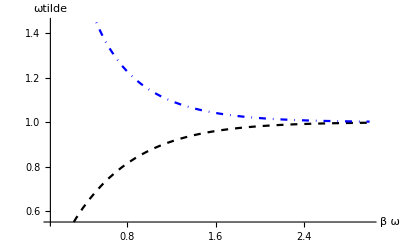

```mathematica
Plot[{√Tanh[θ5],√Coth[θ5]},{θ5,0.1,3},AxesLabel->{"β ω","ωtilde"},PlotStyle->{{Black,Dashed},{Blue,DotDashed}},LabelStyle->Black,Ticks->None]
```

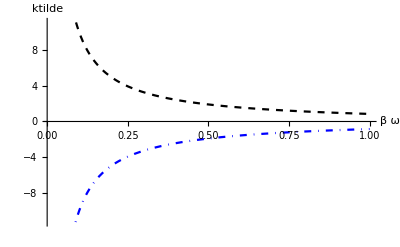

```mathematica
Plot[{Csch[θ5],-Csch[θ5]},{θ5,0.01,1},AxesLabel->{"β ω","ktilde
"},PlotStyle->{{Black,Dashed},{Blue,DotDashed}},LabelStyle->Black,Ticks->None]
```

The  ωptilde and ktilde as a function of  the SDS temperatures . The dashed and dot-dashed curves correspond to l<n and l>n cases,respectively.

### Figure 6: The Quickest Case in SDS

```mathematica
ClearAll[ω,ωp,k,τ,bminus,bplus,bplusdot,bminusdot,A11,A12,A22,ReA11,ReA12,ReA22,ReA12sqr,ImA12,ImA12sqr,ωtilde,ktilde,τtilde,η]
```

The quickest case of thermalization occurs when the values of ωtilde, ktilde,τtilde of our special discrete set have the values:

```mathematica
{ωtilde,ktilde,τtilde}={1/√3,4/3,(√3)/4}
```

{1/(√3),4/3,(√3)/4}

For convenience, let  ω=1.

```mathematica
ω=1
```

1

Then

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{1/(√3),4/3,(√3 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

3

Now we can obtain bplus, bminus, bplusdot, and bminusdot in terms of these values.

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{√(2-Cos[(2 t)/(√3)]),(√(2+Cos[2 √3 t]))/(√3),Sin[(2 t)/(√3)]/(√(6-3 Cos[(2 t)/(√3)])),-Sin[2 √3 t]/(√(2+Cos[2 √3 t]))}

Now we can separate the real and imaginary parts of A_ij.

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//FullSimplify
```

{1/2 (1/(2-Cos[(2 t)/(√3)])-3/(2+Cos[2 √3 t])),(Sin[(2 t)/(√3)]/(-2+Cos[(2 t)/(√3)])-(3 Sin[2 √3 t])/(2+Cos[2 √3 t]))/(2 √3)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//FullSimplify
```

{1/2 (1/(2-Cos[(2 t)/(√3)])+3/(2+Cos[2 √3 t])),(Sin[(2 t)/(√3)]/(-2+Cos[(2 t)/(√3)])+(3 Sin[2 √3 t])/(2+Cos[2 √3 t]))/(2 √3),1/2 (1/(2-Cos[(2 t)/(√3)])+3/(2+Cos[2 √3 t])),(Sin[(2 t)/(√3)]/(-2+Cos[(2 t)/(√3)])+(3 Sin[2 √3 t])/(2+Cos[2 √3 t]))/(2 √3)}

The real and imaginary parts of the A_12^2 are obtained by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//FullSimplify
```

1/12 (4+6/(-2+Cos[(2 t)/(√3)])^2-5/(-2+Cos[(2 t)/(√3)])+54/(2+Cos[2 √3 t])^2-(3 (15+4 Cos[(2 t)/(√3)]+2 Cos[(4 t)/(√3)]))/(2+Cos[2 √3 t]))

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//FullSimplify
```

-((-4+3 Cos[(2 t)/(√3)]+Cos[2 √3 t]) (2 Sin[(2 t)/(√3)]-2 Sin[(4 t)/(√3)]-Sin[(8 t)/(√3)]+6 Sin[2 √3 t]))/(2 √3 (-2+Cos[(2 t)/(√3)])^2 (2+Cos[2 √3 t])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//FullSimplify
```

{1/3 (-4+Cos[(2 t)/(√3)]+(3 (19-8 Cos[(2 t)/(√3)]+Cos[(4 t)/(√3)]))/(8-3 Cos[(2 t)/(√3)]+Cos[2 √3 t])),(√3 (-Sin[(2 t)/(√3)]+Sin[2 √3 t]))/(8-3 Cos[(2 t)/(√3)]+Cos[2 √3 t]),4/3-1/3 Cos[(2 t)/(√3)]-(13-8 Cos[(2 t)/(√3)]+Cos[(4 t)/(√3)])/(8-3 Cos[(2 t)/(√3)]+Cos[2 √3 t])}

Now the initial values of X, Y, and Z, when when t=0 be Xi, Yi, and Zi.

```mathematica
{Xi,Yi,Zi}={X,Y,Z}/.t->0//FullSimplify
```

{1,0,0}

And the final values of X, Y, and Z, when when t = T be Xf, Yf, and Zf .

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{17/15,0,-8/15}

```mathematica
Show[{ParametricPlot3D[{X,Y,Z},{t,0,τ},PlotStyle->Black,BoxRatios->{1,1,1},Ticks->None,AxesLabel->{"X","Y","Z"}]},{ParametricPlot3D[{Coth[θ],0,-Csch[θ]},{θ,0,10},PlotStyle->Red],Graphics3D[{Blue,PointSize[0.03],Point[{Xi,Yi,Zi}],Green,PointSize[0.03],Point[{Xf,Yf,Zf}]}]},LabelStyle->Black]
```

-Graphics3D-

This illustrates the finite-time thermalization of oscillator 1 to the thermal state at β = k_B/E_glog 2, starting from the ground state. The blue and green dots denote the initial and final states of the system.

### Figure 6:

The SDS does not exactly thermalize our system to arbitrary temperatures. But we can always find elements of SDS arbitrarily close to the target temperature. We can understand this by plotting  the evolution of the density matrix for different values of {n,l}.

```mathematica
ClearAll[ω,ωp,k,τ,bminus,bplus,bplusdot,bminusdot,A11,A12,A22,ReA11,ReA12,ReA22,ReA12sqr,ImA12,ImA12sqr,ωtilde,ktilde,τtilde,η]
```

```mathematica
ω=1
```

1

### (a) {n, l} = {12, 11}

Here we will visualize the evolution toward the thermal state for (n,l) = (12,11) to the target inverse temperature β = k_B/E_g π.

```mathematica
{n,l}={12,11}
```

{12,11}

The corresponding values of β and the dimensionless parameters become:

```mathematica
{β,ωtilde,ktilde,τtilde}={Log[(n+l+1)/(n-l)],√((2l+1)/(2n+1)),(2(n-l)(n+l+1))/((2l+1)(2n+1)),1/4 √((2l+1)(2n+1))}
```

{Log[24],(√23)/5,48/575,(5 √23)/4}

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{(√23)/5,48/575,(5 √23 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

25/23

The corresponding values of bplus, bminus, bplusdot, and bminusdot :

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{(√(24-Cos[(2 √23 t)/5]))/(√23),1/5 √(24+Cos[(10 t)/(√23)]),Sin[(2 √23 t)/5]/(5 √(24-Cos[(2 √23 t)/5])),-Sin[(10 t)/(√23)]/(√23 √(24+Cos[(10 t)/(√23)]))}

The real and imaginary parts of A_ij :

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//FullSimplify
```

{-25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5])),(-(25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])+(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))/(10 √23)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//FullSimplify
```

{25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5])),((25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])+(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))/(10 √23),25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5])),((25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])+(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))/(10 √23)}

The real and imaginary parts of (A_12)^2 are given by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//Simplify
```

-((-575 (-48+23 Cos[(10 t)/(√23)]+25 Cos[(2 √23 t)/5])^2+(25 (-24+Cos[(2 √23 t)/5]) Sin[(10 t)/(√23)]-23 (24+Cos[(10 t)/(√23)]) Sin[(2 √23 t)/5])^2)/(2300 (24+Cos[(10 t)/(√23)])^2 (-24+Cos[(2 √23 t)/5])^2))

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//FullSimplify
```

((-48+23 Cos[(10 t)/(√23)]+25 Cos[(2 √23 t)/5]) (24 Sin[(4 t)/(5 √23)]-600 Sin[(10 t)/(√23)]+Sin[(96 t)/(5 √23)]-552 Sin[(2 √23 t)/5]))/(10 √23 (24+Cos[(10 t)/(√23)])^2 (-24+Cos[(2 √23 t)/5])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//Simplify
```

{(1324227+576 Cos[(4 t)/(5 √23)]-1152 Cos[(10 t)/(√23)]+Cos[(96 t)/(5 √23)]-1152 Cos[(2 √23 t)/5])/(1150 (1152+23 Cos[(10 t)/(√23)]-25 Cos[(2 √23 t)/5])),-((5 √23 (Sin[(42 t)/(5 √23)]+2304 Sin[(10 t)/(√23)]-Sin[(54 t)/(5 √23)]-96 Sin[(96 t)/(5 √23)]+48 Sin[(20 t)/(√23)]+Sin[(142 t)/(5 √23)]-Sin[(146 t)/(5 √23)]-2304 Sin[(2 √23 t)/5]+48 Sin[(4 √23 t)/5]))/(4 (24+Cos[(10 t)/(√23)]) (1152+23 Cos[(10 t)/(√23)]-25 Cos[(2 √23 t)/5]) (-24+Cos[(2 √23 t)/5]))),-((25/(2 (24+Cos[(10 t)/(√23)]))+23/(2 (-24+Cos[(2 √23 t)/5])))^2+((25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])-(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))^2/2300)/(2 (25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5]))))}

Now the initial values of X, Y, and Z, when when t = 0 be Xi, Yi, and Zi .

```mathematica
{Xi,Yi,Zi}={X,Y,Z}/.t->0//FullSimplify
```

{1,0,0}

And the final values of X, Y, and Z, when when t=T be Xf, Yf, and Zf.

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{331777/331775,0,-1152/331775}

```mathematica
Show[{ParametricPlot3D[{X,Y,Z},{t,0,τ},PlotStyle->Black,BoxRatios->{1, 1, 1},Ticks->None,AxesLabel->{"X","Y","Z"}]},{ParametricPlot3D[{Coth[θ],0,-Csch[θ]},{θ,0,10},PlotStyle->Red],Graphics3D[{Blue,PointSize[0.03],Point[{Xi,Yi,Zi}],Red,PointSize[0.03],Point[{Xf,Yf,Zf}]}],Graphics3D[{Green,PointSize[0.03],Point[{Coth[2π],0,-Csch[2π]}]}]},LabelStyle->Black]
```

-Graphics3D-

Evolution toward the thermal state for (n,l) = (12,11) to the target inverse temperature β = k_B/E_g π. The exact thermal state corresponding to this value is marked by a green dot, while the approximate thermal state is indicated by a red dot; both lie on the thermal curve.

### (a) {n, l} = {24, 22}

Now let us visualize the evolution toward the thermal state for (n, l) = (24, 22) to the target inverse temperature β = k_B/E_g π.

```mathematica
{n,l}={24,22}
```

{24,22}

The corresponding values of β and the dimensionless parameters become:

```mathematica
{β,ωtilde,ktilde,τtilde}={Log[(n+l+1)/(n-l)],√((2l+1)/(2n+1)),(2(n-l)(n+l+1))/((2l+1)(2n+1)),1/4 √((2l+1)(2n+1))}
```

{Log[47/2],(3 √5)/7,188/2205,(21 √5)/4}

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{(3 √5)/7,188/2205,(21 √5 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

49/45

The corresponding values of bplus,bminus,bplusdot,and bminusdot are:

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{(√(47-2 Cos[(6 √5 t)/7]))/(3 √5),1/7 √(47+2 Cos[(14 t)/(3 √5)]),(2 Sin[(6 √5 t)/7])/(7 √(47-2 Cos[(6 √5 t)/7])),-(2 Sin[(14 t)/(3 √5)])/(3 √5 √(47+2 Cos[(14 t)/(3 √5)]))}

The real and imaginary parts of A_ij are:

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//FullSimplify
```

{-49/(94+4 Cos[(14 t)/(3 √5)])+45/(94-4 Cos[(6 √5 t)/7]),(-(49 Sin[(14 t)/(3 √5)])/(47+2 Cos[(14 t)/(3 √5)])+(45 Sin[(6 √5 t)/7])/(-47+2 Cos[(6 √5 t)/7]))/(21 √5)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//FullSimplify
```

{49/(94+4 Cos[(14 t)/(3 √5)])+45/(94-4 Cos[(6 √5 t)/7]),((49 Sin[(14 t)/(3 √5)])/(47+2 Cos[(14 t)/(3 √5)])+(45 Sin[(6 √5 t)/7])/(-47+2 Cos[(6 √5 t)/7]))/(21 √5),49/(94+4 Cos[(14 t)/(3 √5)])+45/(94-4 Cos[(6 √5 t)/7]),((49 Sin[(14 t)/(3 √5)])/(47+2 Cos[(14 t)/(3 √5)])+(45 Sin[(6 √5 t)/7])/(-47+2 Cos[(6 √5 t)/7]))/(21 √5)}

The real and imaginary parts of (A_12)^2 are given by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//Simplify
```

(8820 (-94+45 Cos[(14 t)/(3 √5)]+49 Cos[(6 √5 t)/7])^2-4 (49 (47-2 Cos[(6 √5 t)/7]) Sin[(14 t)/(3 √5)]+45 (47+2 Cos[(14 t)/(3 √5)]) Sin[(6 √5 t)/7])^2)/(8820 (47+2 Cos[(14 t)/(3 √5)])^2 (47-2 Cos[(6 √5 t)/7])^2)

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//Simplify
```

((15 √(47+2 Cos[(14 t)/(3 √5)])-7 √5 √(47-2 Cos[(6 √5 t)/7])) (15 √(47+2 Cos[(14 t)/(3 √5)])+7 √5 √(47-2 Cos[(6 √5 t)/7])) (94 Sin[(8 t)/(21 √5)]-2303 Sin[(14 t)/(3 √5)]+4 Sin[(188 t)/(21 √5)]-2115 Sin[(6 √5 t)/7]))/(105 √5 (47+2 Cos[(14 t)/(3 √5)])^2 (47-2 Cos[(6 √5 t)/7])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//Simplify
```

{(4868648+2209 Cos[(8 t)/(21 √5)]-4418 Cos[(14 t)/(3 √5)]+4 Cos[(188 t)/(21 √5)]-4418 Cos[(6 √5 t)/7])/(2205 (2209+45 Cos[(14 t)/(3 √5)]-49 Cos[(6 √5 t)/7])),1/(210 √5)((490 Sin[(14 t)/(3 √5)])/(47+2 Cos[(14 t)/(3 √5)])+((15 √(47+2 Cos[(14 t)/(3 √5)])-7 √5 √(47-2 Cos[(6 √5 t)/7])) (15 √(47+2 Cos[(14 t)/(3 √5)])+7 √5 √(47-2 Cos[(6 √5 t)/7])) (94 Sin[(8 t)/(21 √5)]-2303 Sin[(14 t)/(3 √5)]+4 Sin[(188 t)/(21 √5)]-2115 Sin[(6 √5 t)/7]))/((47+2 Cos[(14 t)/(3 √5)]) (2209+45 Cos[(14 t)/(3 √5)]-49 Cos[(6 √5 t)/7]) (-47+2 Cos[(6 √5 t)/7]))+(450 Sin[(6 √5 t)/7])/(-47+2 Cos[(6 √5 t)/7])),-((49/(94+4 Cos[(14 t)/(3 √5)])+45/(-94+4 Cos[(6 √5 t)/7]))^2+((49 Sin[(14 t)/(3 √5)])/(47+2 Cos[(14 t)/(3 √5)])-(45 Sin[(6 √5 t)/7])/(-47+2 Cos[(6 √5 t)/7]))^2/2205)/(2 (49/(94+4 Cos[(14 t)/(3 √5)])+45/(94-4 Cos[(6 √5 t)/7])))}

Now the initial values of X, Y, and Z, when when t=0 be Xi, Yi, and Zi.

```mathematica
{Xi,Yi,Zi}={X,Y,Z}/.t->0//FullSimplify
```

{1,0,0}

And the final values of X, Y, and Z, when t=τ be Xf, Yf, and Zf.

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{4879697/4879665,0,-17672/4879665}

```mathematica
Show[{ParametricPlot3D[{X,Y,Z},{t,0,τ},PlotStyle->Black,BoxRatios->{1, 1, 1},Ticks->None,AxesLabel->{"X","Y","Z"}]},{ParametricPlot3D[{Coth[θ],0,-Csch[θ]},{θ,0,10},PlotStyle->Red],Graphics3D[{Blue,PointSize[0.03],Point[{Xi,Yi,Zi}],Red,PointSize[0.03],Point[{Xf,Yf,Zf}]}],Graphics3D[{Green,PointSize[0.03],Point[{Coth[2π],0,-Csch[2π]}]}]},LabelStyle->Black]
```

-Graphics3D-

Evolution toward the thermal state for (n,l) = (24,22) to the target inverse temperature β = k_B/E_g π. The exact thermal state corresponding to this value is marked by a green dot, while the approximate thermal state is indicated by a red dot; both lie on the thermal curve.

### (c) {n, l} = {36, 33}

Now let us visualize the evolution toward the thermal state for (n, l) = (36, 33) to the target inverse temperature β = k_B/E_g π.

```mathematica
{n, l} = {36, 33}
```

{36,33}

The corresponding values of β and the dimensionless parameters become:

```mathematica
{β,ωtilde,ktilde,τtilde}={Log[(n+l+1)/(n-l)],√((2l+1)/(2n+1)),(2(n-l)(n+l+1))/((2l+1)(2n+1)),1/4 √((2l+1)(2n+1))}
```

{Log[70/3],√(67/73),420/4891,(√4891)/4}

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{√(67/73),420/4891,(√4891 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

73/67

The corresponding values of bplus,bminus,bplusdot,bminusdot, and the real and imaginary parts of A_ij :

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{(√(70-3 Cos[2 √(67/73) t]))/(√67),(√(70+3 Cos[2 √(73/67) t]))/(√73),(3 Sin[2 √(67/73) t])/(√73 √(70-3 Cos[2 √(67/73) t])),-(3 Sin[2 √(73/67) t])/(√67 √(70+3 Cos[2 √(73/67) t]))}

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//FullSimplify
```

{67/(140-6 Cos[2 √(67/73) t])-73/(140+6 Cos[2 √(73/67) t]),(3 ((67 Sin[2 √(67/73) t])/(-70+3 Cos[2 √(67/73) t])-(73 Sin[2 √(73/67) t])/(70+3 Cos[2 √(73/67) t])))/(2 √4891)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//Simplify
```

{67/(140-6 Cos[2 √(67/73) t])+73/(140+6 Cos[2 √(73/67) t]),(3 ((67 Sin[2 √(67/73) t])/(-70+3 Cos[2 √(67/73) t])+(73 Sin[2 √(73/67) t])/(70+3 Cos[2 √(73/67) t])))/(2 √4891),67/(140-6 Cos[2 √(67/73) t])+73/(140+6 Cos[2 √(73/67) t]),(3 ((67 Sin[2 √(67/73) t])/(-70+3 Cos[2 √(67/73) t])+(73 Sin[2 √(73/67) t])/(70+3 Cos[2 √(73/67) t])))/(2 √4891)}

The real and imaginary parts of (A_12)^2 are given by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//Simplify
```

(44019 (-140+73 Cos[2 √(67/73) t]+67 Cos[2 √(73/67) t])^2-9 (67 (70+3 Cos[2 √(73/67) t]) Sin[2 √(67/73) t]+73 (70-3 Cos[2 √(67/73) t]) Sin[2 √(73/67) t])^2)/(19564 (70-3 Cos[2 √(67/73) t])^2 (70+3 Cos[2 √(73/67) t])^2)

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//Simplify
```

(3 (73 √67 √(70-3 Cos[2 √(67/73) t])-67 √73 √(70+3 Cos[2 √(73/67) t])) (73 √67 √(70-3 Cos[2 √(67/73) t])+67 √73 √(70+3 Cos[2 √(73/67) t])) (4690 Sin[2 √(67/73) t]+5110 Sin[2 √(73/67) t]-210 Sin[(12 t)/(√4891)]-9 Sin[(280 t)/(√4891)]))/(9782 √4891 (70-3 Cos[2 √(67/73) t])^2 (70+3 Cos[2 √(73/67) t])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//Simplify
```

{(95819743-88200 Cos[2 √(67/73) t]-88200 Cos[2 √(73/67) t]+44100 Cos[(12 t)/(√4891)]+81 Cos[(280 t)/(√4891)])/(9782 (9800-219 Cos[2 √(67/73) t]+201 Cos[2 √(73/67) t])),1/(19564 √4891)3 (9782 ((67 Sin[2 √(67/73) t])/(-70+3 Cos[2 √(67/73) t])+(73 Sin[2 √(73/67) t])/(70+3 Cos[2 √(73/67) t]))-(2 (73 √67 √(70-3 Cos[2 √(67/73) t])-67 √73 √(70+3 Cos[2 √(73/67) t])) (73 √67 √(70-3 Cos[2 √(67/73) t])+67 √73 √(70+3 Cos[2 √(73/67) t])) (4690 Sin[2 √(67/73) t]+5110 Sin[2 √(73/67) t]-210 Sin[(12 t)/(√4891)]-9 Sin[(280 t)/(√4891)]))/((-70+3 Cos[2 √(67/73) t]) (-9800+219 Cos[2 √(67/73) t]-201 Cos[2 √(73/67) t]) (70+3 Cos[2 √(73/67) t]))),-((67/(140-6 Cos[2 √(67/73) t])-73/(140+6 Cos[2 √(73/67) t]))^2+(9 ((67 Sin[2 √(67/73) t])/(-70+3 Cos[2 √(67/73) t])-(73 Sin[2 √(73/67) t])/(70+3 Cos[2 √(73/67) t]))^2)/19564)/(2 (67/(140-6 Cos[2 √(67/73) t])+73/(140+6 Cos[2 √(73/67) t])))}

Now the initial values of X, Y, and Z, when when t=0 be Xi, Yi, and Zi.

```mathematica
{Xi,Yi,Zi}={X,Y,Z}/.t->0//FullSimplify
```

{1,0,0}

And the final values of X, Y, and Z, when t=τ be Xf, Yf, and Zf.

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{24010081/24009919,0,-88200/24009919}

```mathematica
Show[{ParametricPlot3D[{X,Y,Z},{t,0,τ},PlotStyle->Black,BoxRatios->{1, 1, 1},Ticks->None,AxesLabel->{"X","Y","Z"}]},{ParametricPlot3D[{Coth[θ],0,-Csch[θ]},{θ,0,10},PlotStyle->Red],Graphics3D[{Blue,PointSize[0.03],Point[{Xi,Yi,Zi}],Red,PointSize[0.03],Point[{Xf,Yf,Zf}]}],Graphics3D[{Green,PointSize[0.03],Point[{Coth[2π],0,-Csch[2π]}]}]},LabelStyle->Black]
```

-Graphics3D-

Evolution toward the thermal state for (n,l) = (36,33) to the target inverse temperature β = k_B/E_g π. The exact thermal state corresponding to this value is marked by a green dot, while the approximate thermal state is indicated by a red dot; both lie on the thermal curve.

### (d) {n, l} = {48, 44}

Now let us visualize the evolution toward the thermal state for (n, l) = (48, 44) to the target inverse temperature β = k_B/E_g π.

```mathematica
{n,l}={48,44}
```

{48,44}

The corresponding values of β and the dimensionless parameters become:

```mathematica
{β,ωtilde,ktilde,τtilde}={Log[(n+l+1)/(n-l)],√((2l+1)/(2n+1)),(2(n-l)(n+l+1))/((2l+1)(2n+1)),1/4 √((2l+1)(2n+1))}
```

{Log[93/4],√(89/97),744/8633,(√8633)/4}

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{√(89/97),744/8633,(√8633 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

97/89

The corresponding values of bplus, bminus, bplusdot, bminusdot, and the real and imaginary parts of A_ij :

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{(√(93-4 Cos[2 √(89/97) t]))/(√89),(√(93+4 Cos[2 √(97/89) t]))/(√97),(4 Sin[2 √(89/97) t])/(√97 √(93-4 Cos[2 √(89/97) t])),-(4 Sin[2 √(97/89) t])/(√89 √(93+4 Cos[2 √(97/89) t]))}

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//Simplify
```

{89/(186-8 Cos[2 √(89/97) t])-97/(186+8 Cos[2 √(97/89) t]),(2 ((89 Sin[2 √(89/97) t])/(-93+4 Cos[2 √(89/97) t])-(97 Sin[2 √(97/89) t])/(93+4 Cos[2 √(97/89) t])))/(√8633)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//Simplify
```

{89/(186-8 Cos[2 √(89/97) t])+97/(186+8 Cos[2 √(97/89) t]),(2 ((89 Sin[2 √(89/97) t])/(-93+4 Cos[2 √(89/97) t])+(97 Sin[2 √(97/89) t])/(93+4 Cos[2 √(97/89) t])))/(√8633),89/(186-8 Cos[2 √(89/97) t])+97/(186+8 Cos[2 √(97/89) t]),(2 ((89 Sin[2 √(89/97) t])/(-93+4 Cos[2 √(89/97) t])+(97 Sin[2 √(97/89) t])/(93+4 Cos[2 √(97/89) t])))/(√8633)}

The real and imaginary parts of (A_12)^2 are given by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//Simplify
```

(138128 (-186+97 Cos[2 √(89/97) t]+89 Cos[2 √(97/89) t])^2-16 (89 (93+4 Cos[2 √(97/89) t]) Sin[2 √(89/97) t]+97 (93-4 Cos[2 √(89/97) t]) Sin[2 √(97/89) t])^2)/(34532 (93-4 Cos[2 √(89/97) t])^2 (93+4 Cos[2 √(97/89) t])^2)

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//Simplify
```

(2 (97 √89 √(93-4 Cos[2 √(89/97) t])-89 √97 √(93+4 Cos[2 √(97/89) t])) (97 √89 √(93-4 Cos[2 √(89/97) t])+89 √97 √(93+4 Cos[2 √(97/89) t])) (8277 Sin[2 √(89/97) t]+9021 Sin[2 √(97/89) t]-4 (93 Sin[(16 t)/(√8633)]+4 Sin[(372 t)/(√8633)])))/(8633 √8633 (93-4 Cos[2 √(89/97) t])^2 (93+4 Cos[2 √(97/89) t])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//Simplify
```

{(74632413-69192 Cos[2 √(89/97) t]-69192 Cos[2 √(97/89) t]+34596 Cos[(16 t)/(√8633)]+64 Cos[(372 t)/(√8633)])/(8633 (8649-194 Cos[2 √(89/97) t]+178 Cos[2 √(97/89) t])),1/(8633 √8633)(17266 ((89 Sin[2 √(89/97) t])/(-93+4 Cos[2 √(89/97) t])+(97 Sin[2 √(97/89) t])/(93+4 Cos[2 √(97/89) t]))-((97 √89 √(93-4 Cos[2 √(89/97) t])-89 √97 √(93+4 Cos[2 √(97/89) t])) (97 √89 √(93-4 Cos[2 √(89/97) t])+89 √97 √(93+4 Cos[2 √(97/89) t])) (8277 Sin[2 √(89/97) t]+9021 Sin[2 √(97/89) t]-4 (93 Sin[(16 t)/(√8633)]+4 Sin[(372 t)/(√8633)])))/((-93+4 Cos[2 √(89/97) t]) (-8649+194 Cos[2 √(89/97) t]-178 Cos[2 √(97/89) t]) (93+4 Cos[2 √(97/89) t]))),-((89/(186-8 Cos[2 √(89/97) t])-97/(186+8 Cos[2 √(97/89) t]))^2+(4 ((89 Sin[2 √(89/97) t])/(-93+4 Cos[2 √(89/97) t])-(97 Sin[2 √(97/89) t])/(93+4 Cos[2 √(97/89) t]))^2)/8633)/(2 (89/(186-8 Cos[2 √(89/97) t])+97/(186+8 Cos[2 √(97/89) t])))}

Now the initial values of X, Y, and Z, when when t=0 be Xi, Yi, and Zi.

```mathematica
{Xi,Yi,Zi}={X,Y,Z}/.t->0//FullSimplify
```

{1,0,0}

And the final values of X, Y, and Z, when t=τ be Xf, Yf, and Zf.

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{74805457/74804945,0,-276768/74804945}

```mathematica
Show[{ParametricPlot3D[{X,Y,Z},{t,0,τ},PlotStyle->Black,BoxRatios->{1, 1, 1},Ticks->None,AxesLabel->{"X","Y","Z"}]},{ParametricPlot3D[{Coth[θ],0,-Csch[θ]},{θ,0,10},PlotStyle->Red],Graphics3D[{Blue,PointSize[0.03],Point[{Xi,Yi,Zi}],Red,PointSize[0.03],Point[{Xf,Yf,Zf}]}],Graphics3D[{Green,PointSize[0.03],Point[{Coth[2π],0,-Csch[2π]}]}]},LabelStyle->Black]
```

-Graphics3D-

Evolution toward the thermal state for (n,l) = (48,44) to the target inverse temperature β = k_B/E_g π. The exact thermal state corresponding to this value is marked by a green dot, while the approximate thermal state is indicated by a red dot; both lie on the thermal curve.

### Accuracy and Thermalization time for {n,l}={12,11}

```mathematica
ClearAll["Global`*"]
```

```mathematica
{n,l}={12,11}
```

{12,11}

We have Eg/(k_B T_nl)=(Eg β)/k_B=Log[(1+l+n)/Abs[-l+n]].  So β_nl becomes:

```mathematica
N[βnl=kB/Eg Log[(1+l+n)/Abs[-l+n]]]
```

(3.17805 kB)/Eg

The target temperature here is  β=kB/Eg π.

```mathematica
β=kB/Eg π
```

(kB π)/Eg

The difference between target temperature and achieved temperature is:

```mathematica
δβ=β-βnl
```

(kB π)/Eg-(kB Log[24])/Eg

The accuracy, in percentage, can be calculated by:

```mathematica
N[δβ/β 100]//FullSimplify
```

-1.1606

The dimensionless time parameter τtilde takes the value:

```mathematica
N[τtilde=1/4 √((1+2 l) (1+2 n))]
```

5.99479

### Accuracy and Thermalization time for {n,l}={24,22}

```mathematica
ClearAll["Global`*"]
```

```mathematica
{n,l}={24,22}
```

{24,22}

We have Eg/(k_B T_nl)=(Eg β)/k_B=Log[(1+l+n)/Abs[-l+n]].  So β_nl becomes:

```mathematica
N[βnl=kB/Eg Log[(1+l+n)/Abs[-l+n]]]
```

(3.157 kB)/Eg

The target temperature here is  β=kB/Eg π.

```mathematica
β=kB/Eg π
```

(kB π)/Eg

The difference between target temperature and achieved temperature is:

```mathematica
δβ=β-βnl
```

(kB π)/Eg-(kB Log[47/2])/Eg

The accuracy, in percentage, can be calculated by:

```mathematica
N[δβ/β 100]//FullSimplify
```

-0.490444

The dimensionless time parameter τtilde takes the value:

```mathematica
N[τtilde=1/4 √((1+2 l) (1+2 n))]
```

11.7394

### Accuracy and Thermalization time for {n,l}={36,33}

```mathematica
ClearAll["Global`*"]
```

```mathematica
{n,l}={36,33}
```

{36,33}

We have Eg/(k_B T_nl)=(Eg β)/k_B=Log[(1+l+n)/Abs[-l+n]].  So β_nl becomes:

```mathematica
N[βnl=kB/Eg Log[(1+l+n)/Abs[-l+n]]]
```

(3.14988 kB)/Eg

The target temperature here is  β=kB/Eg π.

```mathematica
β=kB/Eg π
```

(kB π)/Eg

The difference between target temperature and achieved temperature is:

```mathematica
δβ=β-βnl
```

(kB π)/Eg-(kB Log[70/3])/Eg

The accuracy, in percentage, can be calculated by:

```mathematica
N[δβ/β 100]//FullSimplify
```

-0.263888

The dimensionless time parameter τtilde takes the value:

```mathematica
N[τtilde=1/4 √((1+2 l) (1+2 n))]
```

17.4839

### Accuracy and Thermalization time for {n,l}={48,44}

```mathematica
ClearAll["Global`*"]
```

```mathematica
{n,l}={48,44}
```

{48,44}

We have Eg/(k_B T_nl)=(Eg β)/k_B=Log[(1+l+n)/Abs[-l+n]].  So β_nl becomes:

```mathematica
N[βnl=kB/Eg Log[(1+l+n)/Abs[-l+n]]]
```

(3.14631 kB)/Eg

The target temperature here is  β=kB/Eg π.

```mathematica
β=kB/Eg π
```

(kB π)/Eg

The difference between target temperature and achieved temperature is:

```mathematica
δβ=β-βnl
```

(kB π)/Eg-(kB Log[93/4])/Eg

The accuracy, in percentage, can be calculated by:

```mathematica
N[δβ/β 100]//FullSimplify
```

-0.150003

The dimensionless time parameter τtilde takes the value:

```mathematica
N[τtilde=1/4 √((1+2 l) (1+2 n))]
```

23.2285

### Accuracy and Thermalization time for {n,l}={60,55}

```mathematica
ClearAll["Global`*"]
```

```mathematica
{n,l}={60,55}
```

{60,55}

We have Eg/(k_B T_nl)=(Eg β)/k_B=Log[(1+l+n)/Abs[-l+n]].  So β_nl becomes:

```mathematica
N[βnl=kB/Eg Log[(1+l+n)/Abs[-l+n]]]
```

(3.14415 kB)/Eg

The target temperature here is  β=kB/Eg π.

```mathematica
β=kB/Eg π
```

(kB π)/Eg

The difference between target temperature and achieved temperature is:

```mathematica
δβ=β-βnl
```

(kB π)/Eg-(kB Log[116/5])/Eg

The accuracy, in percentage, can be calculated by:

```mathematica
N[δβ/β 100]//FullSimplify
```

-0.0814754

The dimensionless time parameter τtilde takes the value:

```mathematica
N[τtilde=1/4 √((1+2 l) (1+2 n))]
```

28.973

### Table 1:

So the SDS temperatures don’t include every possible temperature. But they do form a countably dense subset of the positive real numbers, which represent all possible temperatures.

```mathematica
Column[{Grid[{{Style["(l,n)",Bold],Style["E_gβ_nl/k_B",Bold],Style["δβ/β",Bold],Style["τtilde",Bold]},{"(12,11)",3.178,"1.16%",5.99},{"(24,22)",3.157,".49%",11.74},{"(36,33)",3.149,".26%",17.48},{"(48,44)",3.146,".15%",23.23},{"(60,55)",3.144,".08%",28.97}},Frame->All,Spacings->{3,1},ItemStyle->{FontFamily->"Times",FontSize->20}]}]
```

(l,n) | E_gβ_nl/k_B | δβ/β | τtilde
(12,11) | 3.178 | 1.16% | 5.99
(24,22) | 3.157 | .49% | 11.74
(36,33) | 3.149 | .26% | 17.48
(48,44) | 3.146 | .15% | 23.23
(60,55) | 3.144 | .08% | 28.97

TABLE 1 : List of SDS approximations to β = π k_B/E_g. As one moves down the list, the approximation error in temperature decreases by roughly a factor of two with each step. However, this improved accuracy comes at the cost of longer thermalization times, which in this example is scaling roughly inversely with the %-error in temperature.

### Average Energy

Now we will look at the average energy of the oscillator.

```mathematica
m=1
```

1

Average energy is given by the expectation value of Hamiltonian, U(t) = <H0>

```mathematica
H0Exp= Σpp/2+ (ω^2 Σxx)/2//FullSimplify
```

1/2 (Σpp+Σxx ω^2)

So the average energy is equal to  (E_g(1+X1^2+Y1^2-Z1^2))/(2(X1+Z1)).

### Figure 8(a) : Evolution of U(t) when {n,l} = {1,0}

We shall see the dynamics of average energy U(t) for the case of (n,l)=(1,0).

```mathematica
ω=1
```

1

```mathematica
{n,l}={1,0}
```

{1,0}

The corresponding values of β and the dimensionless parameters become:

```mathematica
{β,ωtilde,ktilde,τtilde}={Log[(n+l+1)/(n-l)],√((2l+1)/(2n+1)),(2(n-l)(n+l+1))/((2l+1)(2n+1)),1/4 √((2l+1)(2n+1))}
```

{Log[2],1/(√3),4/3,(√3)/4}

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{1/(√3),4/3,(√3 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

3

The corresponding values of bplus, bminus, bplusdot, and bminusdot are:

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{√(2-Cos[(2 t)/(√3)]),(√(2+Cos[2 √3 t]))/(√3),Sin[(2 t)/(√3)]/(√(6-3 Cos[(2 t)/(√3)])),-Sin[2 √3 t]/(√(2+Cos[2 √3 t]))}

Separating the real and imaginary parts of A_ij:

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//Simplify
```

{1/2 (1/(2-Cos[(2 t)/(√3)])-3/(2+Cos[2 √3 t])),(Sin[(2 t)/(√3)]/(-2+Cos[(2 t)/(√3)])-(3 Sin[2 √3 t])/(2+Cos[2 √3 t]))/(2 √3)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//Simplify
```

{1/2 (1/(2-Cos[(2 t)/(√3)])+3/(2+Cos[2 √3 t])),(2 Sin[(2 t)/(√3)]+Sin[(4 t)/(√3)]+2 Sin[(8 t)/(√3)]-6 Sin[2 √3 t])/(2 √3 (-2+Cos[(2 t)/(√3)]) (2+Cos[2 √3 t])),1/2 (1/(2-Cos[(2 t)/(√3)])+3/(2+Cos[2 √3 t])),(2 Sin[(2 t)/(√3)]+Sin[(4 t)/(√3)]+2 Sin[(8 t)/(√3)]-6 Sin[2 √3 t])/(2 √3 (-2+Cos[(2 t)/(√3)]) (2+Cos[2 √3 t]))}

The real and imaginary parts of (A_12)^2 are given by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//Simplify
```

-(((6+93 Cos[(2 t)/(√3)]+74 Cos[(4 t)/(√3)]+26 Cos[(8 t)/(√3)]+22 Cos[(10 t)/(√3)]+Cos[(14 t)/(√3)]+76 Cos[2 √3 t]-10 Cos[4 √3 t]) Sin[t/(√3)]^2)/(6 (-2+Cos[(2 t)/(√3)])^2 (2+Cos[2 √3 t])^2))

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//Simplify
```

((-3 √(2-Cos[(2 t)/(√3)])+√3 √(2+Cos[2 √3 t])) (3 √(2-Cos[(2 t)/(√3)])+√3 √(2+Cos[2 √3 t])) (-2 Sin[(2 t)/(√3)]+2 Sin[(4 t)/(√3)]+Sin[(8 t)/(√3)]-6 Sin[2 √3 t]))/(6 √3 (-2+Cos[(2 t)/(√3)])^2 (2+Cos[2 √3 t])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//Simplify
```

{(47-8 Cos[(2 t)/(√3)]+4 Cos[(4 t)/(√3)]+Cos[(8 t)/(√3)]-8 Cos[2 √3 t])/(6 (8-3 Cos[(2 t)/(√3)]+Cos[2 √3 t])),(√3 (-Sin[(2 t)/(√3)]+Sin[2 √3 t]))/(8-3 Cos[(2 t)/(√3)]+Cos[2 √3 t]),(2 (-10-9 Cos[(2 t)/(√3)]-6 Cos[(4 t)/(√3)]+Cos[2 √3 t]) Sin[t/(√3)]^2)/(3 (8-3 Cos[(2 t)/(√3)]+Cos[2 √3 t]))}

The final values of X, Y, and Z, when t = τ be Xf, Yf, and Zf .

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{17/15,0,-8/15}

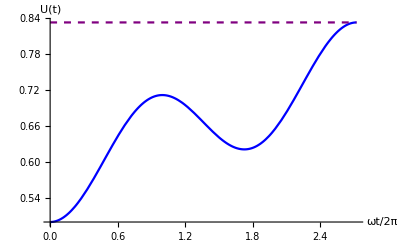

```mathematica
Plot[{(1+X^2+Y^2-Z^2)/(4 (X+Z)),(1+Xf^2+Yf^2-Zf^2)/(4 (Xf+Zf))},{t,0,τ}, PlotStyle->{Blue,{Purple,Dashed}},LabelStyle->Black,Ticks->None,AxesLabel->{"ωt/2π","U(t)"},PlotRange->All]
```

β = k_B/E_g log2 corresponding to (l,n) = (1,0)

### Figure 8(b): Evolution of U(t) for {n,l} = {12,11}

Now we will look at the dynamics of average energy U(t) for the case of (n,l)=(12,11).

```mathematica
ω=1
```

1

```mathematica
{n,l}={12,11}
```

{12,11}

The corresponding values of β and the dimensionless parameters become:

```mathematica
{β,ωtilde,ktilde,τtilde}={Log[(n+l+1)/(n-l)],√((2l+1)/(2n+1)),(2(n-l)(n+l+1))/((2l+1)(2n+1)),1/4 √((2l+1)(2n+1))}
```

{Log[24],(√23)/5,48/575,(5 √23)/4}

```mathematica
{ωp,k,τ}={ω ωtilde,ktilde ω^2,2π τtilde/ω}
```

{(√23)/5,48/575,(5 √23 π)/2}

```mathematica
η=√(1+(2 k)/ωp^2)
```

25/23

The corresponding values of bplus, bminus, bplusdot, and bminusdot are:

```mathematica
{bplus,bminus,bplusdot,bminusdot}={√(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2),√(Cos[η t ωp]^2+(ω^2 Sin[η t ωp]^2)/(η^2  ωp^2)),((ω-ωp) (ω+ωp) Sin[2 t ωp])/(2 ωp √(Cos[t ωp]^2+(ω^2 Sin[t ωp]^2)/ωp^2)),((-2 k+ω^2-ωp^2) Sin[2 t √(1+(2 k)/ωp^2) ωp])/(2 √(1+(2 k)/ωp^2) ωp √(Cos[t √(1+(2 k)/ωp^2) ωp]^2+(ω^2 Sin[t √(1+(2 k)/ωp^2) ωp]^2)/(2 k+ωp^2)))}//FullSimplify
```

{(√(24-Cos[(2 √23 t)/5]))/(√23),1/5 √(24+Cos[(10 t)/(√23)]),Sin[(2 √23 t)/5]/(5 √(24-Cos[(2 √23 t)/5])),-Sin[(10 t)/(√23)]/(√23 √(24+Cos[(10 t)/(√23)]))}

Separating the real and imaginary parts of A_ij:

```mathematica
{ReA12,ImA12}={(ω/(2 bplus^2)-ω/(2 bminus^2)),(- bplusdot/(2bplus)+ bminusdot/(2bminus))}//Simplify
```

{-25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5])),(-(25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])+(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))/(10 √23)}

```mathematica
{ReA11,ImA11,ReA22,ImA22}={ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus),ω/(2 bplus^2)+ω/(2 bminus^2),-bplusdot/(2bplus)-bminusdot/(2bminus)}//Simplify
```

{25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5])),((25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])+(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))/(10 √23),25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5])),((25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])+(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))/(10 √23)}

The real and imaginary parts of (A_12)^2 are given by

```mathematica
ReA12sqr=1/(4 bminus^4 bplus^4)(-bminus^2 bplus^2 (bminusdot bplus-bminus bplusdot)^2+(bminus^2-bplus^2)^2 ω^2)//Simplify
```

-((-575 (-48+23 Cos[(10 t)/(√23)]+25 Cos[(2 √23 t)/5])^2+(25 (-24+Cos[(2 √23 t)/5]) Sin[(10 t)/(√23)]-23 (24+Cos[(10 t)/(√23)]) Sin[(2 √23 t)/5])^2)/(2300 (24+Cos[(10 t)/(√23)])^2 (-24+Cos[(2 √23 t)/5])^2))

```mathematica
ImA12sqr=-(((bminus-bplus) (bminus+bplus) (-bminusdot bplus+bminus bplusdot) ω)/(2 bminus^3 bplus^3))//Simplify
```

((23 √(24+Cos[(10 t)/(√23)])-5 √23 √(24-Cos[(2 √23 t)/5])) (23 √(24+Cos[(10 t)/(√23)])+5 √23 √(24-Cos[(2 √23 t)/5])) (24 Sin[(4 t)/(5 √23)]-600 Sin[(10 t)/(√23)]+Sin[(96 t)/(5 √23)]-552 Sin[(2 √23 t)/5]))/(230 √23 (24+Cos[(10 t)/(√23)])^2 (-24+Cos[(2 √23 t)/5])^2)

Now, as we have obtained the expressions of real and imaginary parts of A_ij, we can find the corresponding X, Y, and Z.

```mathematica
{X,Y,Z}={ReA11-ReA12sqr/(2 ReA11),ImA11-ImA12sqr/(2 ReA11),(-(ReA12^2 + ImA12^2))/(2 ReA11)}//Simplify
```

{(1324227+576 Cos[(4 t)/(5 √23)]-1152 Cos[(10 t)/(√23)]+Cos[(96 t)/(5 √23)]-1152 Cos[(2 √23 t)/5])/(1150 (1152+23 Cos[(10 t)/(√23)]-25 Cos[(2 √23 t)/5])),-((5 √23 (Sin[(42 t)/(5 √23)]+2304 Sin[(10 t)/(√23)]-Sin[(54 t)/(5 √23)]-96 Sin[(96 t)/(5 √23)]+48 Sin[(20 t)/(√23)]+Sin[(142 t)/(5 √23)]-Sin[(146 t)/(5 √23)]-2304 Sin[(2 √23 t)/5]+48 Sin[(4 √23 t)/5]))/(4 (24+Cos[(10 t)/(√23)]) (1152+23 Cos[(10 t)/(√23)]-25 Cos[(2 √23 t)/5]) (-24+Cos[(2 √23 t)/5]))),-((25/(2 (24+Cos[(10 t)/(√23)]))+23/(2 (-24+Cos[(2 √23 t)/5])))^2+((25 Sin[(10 t)/(√23)])/(24+Cos[(10 t)/(√23)])-(23 Sin[(2 √23 t)/5])/(-24+Cos[(2 √23 t)/5]))^2/2300)/(2 (25/(2 (24+Cos[(10 t)/(√23)]))-23/(2 (-24+Cos[(2 √23 t)/5]))))}

The final values of X, Y, and Z, when t = τ be Xf, Yf, and Zf .

```mathematica
{Xf,Yf,Zf}={X,Y,Z}/.t->τ//FullSimplify
```

{331777/331775,0,-1152/331775}

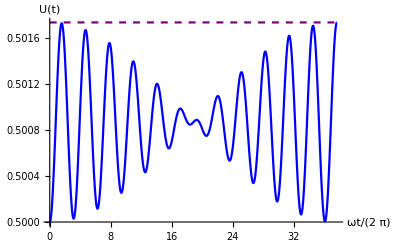

```mathematica
Plot[{(1+X^2+Y^2-Z^2)/(4 (X+Z)),(1+Xf^2+Yf^2-Zf^2)/(4 (Xf+Zf))},{t,0,τ}, PlotStyle->{Blue,{Purple,Dashed}},LabelStyle->Black,Ticks->None,AxesLabel->{"ωt/(2  π)","U(t)"},PlotRange->All]
```

β = k_B/E_g 3.178 corresponding to (l,n) = (12, 11)

### Figure 9(b): Heating and Cooling from Quenching

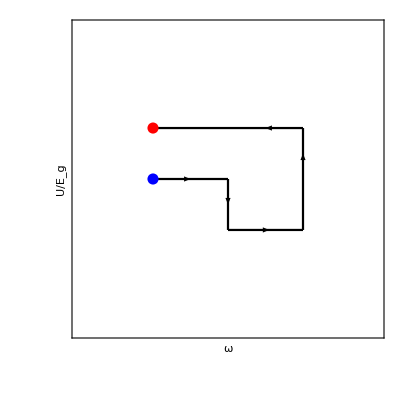

```mathematica
Show[{ContourPlot[y==1,{x,-1,1},{y,-3,3},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}},FrameLabel->{"ω",Rotate["U/E_g",-π/2]},LabelStyle->{Black},FrameTicks->None],ContourPlot[x==1,{x,-1,2},{y,1,-1},ContourStyle->Black],ContourPlot[x==0,{x,-3,3},{y,-1,0},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}],ContourPlot[y==0,{x,-1,0},{y,-3,3},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}],ContourPlot[y==-1,{x,0,1},{y,-3,3},ContourStyle->Black,PlotRange->{{-2,2},{-3,3}}],Graphics[{Black,Arrowheads[0.03],Arrow[{{0.6,1},{0.5,1}}],Arrow[{{-1,0},{-0.5,0}}],Arrow[{{0,0},{0,-0.5}}],Arrow[{{1,0},{1,0.5}}],Arrow[{{0.5,-1},{0.55,-1}}],Blue,PointSize[0.02],Point[{-1,0}],Red,PointSize[0.02],Point[{-1,1}]}]
}]
```

The energy–frequency diagram of oscillator-1, for either heating or cooling, is shown here for the case of heating.